```mathematica
tmn[m_,n_,hp_]:=(2hp+m n-1+Sqrt[4hp(hp+m n-1)+(m-n)^2])/(n^2-1)
cmn[m_,n_,hp_]:=13-6(tmn[m,n,hp]+1/tmn[m,n,hp])
ljk[m_,n_,j_,k_,hp_]:=(j-k tmn[m,n,hp])/Sqrt[tmn[m,n,hp]]
li[m_,n_,hi_,hp_]:=Sqrt[hi+ljk[m,n,1,1,hp]^2/4]
Pmn[m_,n_,h1_,h2_,hp_]:=Product[(2li[m,n,h1,hp]-ljk[m,n,j,k,hp]/2)(-ljk[m,n,j,k,hp]/2)(2li[m,n,h2,hp]-ljk[m,n,j,k,hp]/2)(-ljk[m,n,j,k,hp]/2),{j,-m+1,m-1,2},{k,-n+1,n-1,2}]
itorAmn[m_,n_]:=DeleteCases[Flatten[Table[{a,b},{a,-m+1,m,1},{b,-n+1,n,1}],1],{x_,y_} /; (x==0&&y==0)||(x==m&&y==n)]
Bmn[m_,n_,hp_]:=Times@@(itorAmn[m,n]/.{{a_,b_}->ljk[m,n,a,b,hp]})
Amn[m_,n_,hp_]:=-12(tmn[m,n,hp]^(-1)-tmn[m,n,hp])/((m^2-1)tmn[m,n,hp]^(-1)-(n^2-1)tmn[m,n,hp])/Bmn[m,n,hp]
Rmn[m_,n_,h1_,h2_,hp_]:=Amn[m,n,hp]Pmn[m,n,h1,h2,hp]
gammamn[m_,n_,c_,h1_,h2_,hp_]:=Rmn[m,n,h1,h2,hp]/(c-cmn[m,n,hp])
genmntabinner[q_]:=Cases[Flatten[Table[{m,n},{m,1,q},{n,2,q}],1],{m_,n_}/;(m<n)]
summn[lst_]:=If[lst=={},0,Plus@@Map[#[[1]]*#[[2]]&,lst]]
mod2prod[lst_]:=Plus@@Map[Mod[#[[1]]*#[[2]],2]&,lst]
genmntab[q_,l_]:=Select[Select[Tuples[genmntabinner[q],l],summn[#]==q&],mod2prod[#]==0&]
hpeff[lst_]:=summn[Drop[lst,-1]]
hpefflm1[lst_]:=summn[Drop[lst,-2]]
ceffl[l_,lst_,c_]:=If[l==1,c,cmn[lst[[-2]][[1]],lst[[-2]][[2]],hpefflm1[lst]]]
gammamlnl[l_,lst_,c_,h1_,h2_]:=gammamn[lst[[-1]][[1]],lst[[-1]][[2]],ceffl[l,lst,c],h1,h2,hpeff[lst]]
prodlvl[l_,lst_,c_,h1_,h2_]:=Times@@Table[gammamlnl[j,Take[lst,j],c,h1,h2],{j,1,l}]
chiq[q_,c_,h1_,h2_]:=Plus@@Flatten[Table[Expand[Map[prodlvl[l,#,c,h1,h2]&,genmntab[q,l]]],{l,q/2}]]
chiqfs[q_,c_,h1_,h2_]:=FullSimplify[Plus@@Flatten[Table[FullSimplify[Map[prodlvl[l,#,c,h1,h2]&,genmntab[q,l]]],{l,q/2}]]]
expandinfty[q_,c_,h1_,h2_]:=ReplaceAll[Part[ReplaceAll[Series[chiq[q,c,h1,h2]/.{c->cinv^(-1),h1->h1inv^(-1),h2->h2inv^(-1)},{cinv,0,2},{h1inv,0,0},{h2inv,0,0}]//Normal,{h1inv->h1^(-1),h2inv->h2^(-1)}]//MonomialList,1],{cinv->c^(-1)}]//FullSimplify
flevel[q_,c_,h1_,h2_,z_]:=chiq[q,c,h1,h2]*z^q*Hypergeometric2F1[q,q,2q,z]
perlmutter[n_,c_,h1_,h2_,z_]:=Sum[expandinfty[q,c,h1,h2]*z^q*Hypergeometric2F1[q,q,2q,z],{q,2,n}]
fitzpatrick[c_,h1_,h2_,z_]:=(2h1 h2 z^2 Hypergeometric2F1[2,2,4,z]/c)^2
diff[n_,c_,h1_,h2_,z_]:=perlmutter[n,c,h1,h2,z]-fitzpatrick[c,h1,h2,z]
```

```mathematica
chiq[2,c,h1,h2]
chiq[4,c,h1,h2]
chiq[6,c,h1,h2]
```

(2 h1 h2)/c

(h1 h2)/(55 c)-(h1 h2)/(55 (22/5+c))+(h1^2 h2)/(11 c)-(h1^2 h2)/(11 (22/5+c))+(h1 h2^2)/(11 c)-(h1 h2^2)/(11 (22/5+c))+(5 h1^2 h2^2)/(11 c)-(5 h1^2 h2^2)/(11 (22/5+c))

(h1 h2)/(21021 (-1/2+c))+(6722 h1 h2)/(6585579 c)-(4 h1 h2)/(4851 (22/5+c))+(6 h1 h2)/(17017 (68/7+c))-(6 h1^2 h2)/(7007 (-1/2+c))+(7279 h1^2 h2)/(940797 c)-(26 h1^2 h2)/(4851 (22/5+c))+(5 h1^2 h2)/(2431 (68/7+c))+(32 h1^3 h2)/(21021 (-1/2+c))+(685 h1^3 h2)/(104533 c)-(10 h1^3 h2)/(1617 (22/5+c))+(7 h1^3 h2)/(2431 (68/7+c))-(6 h1 h2^2)/(7007 (-1/2+c))+(7279 h1 h2^2)/(940797 c)-(26 h1 h2^2)/(4851 (22/5+c))+(5 h1 h2^2)/(2431 (68/7+c))+(108 h1^2 h2^2)/(7007 (-1/2+c))+(54367 h1^2 h2^2)/(1881594 c)-(169 h1^2 h2^2)/(4851 (22/5+c))+(175 h1^2 h2^2)/(14586 (68/7+c))-(192 h1^3 h2^2)/(7007 (-1/2+c))+(16605 h1^3 h2^2)/(209066 c)-(65 h1^3 h2^2)/(1617 (22/5+c))+(245 h1^3 h2^2)/(14586 (68/7+c))+(32 h1 h2^3)/(21021 (-1/2+c))+(685 h1 h2^3)/(104533 c)-(10 h1 h2^3)/(1617 (22/5+c))+(7 h1 h2^3)/(2431 (68/7+c))-(192 h1^2 h2^3)/(7007 (-1/2+c))+(16605 h1^2 h2^3)/(209066 c)-(65 h1^2 h2^3)/(1617 (22/5+c))+(245 h1^2 h2^3)/(14586 (68/7+c))+(1024 h1^3 h2^3)/(21021 (-1/2+c))+(2575 h1^3 h2^3)/(209066 c)-(25 h1^3 h2^3)/(539 (22/5+c))+(343 h1^3 h2^3)/(14586 (68/7+c))

```mathematica
chiq[6,c,h1,h2]-(14h1^2+h1)(14h2^2+h2)/(63c(70c+29))-(4h1 h2(c(70h1^2+42h1+8)+29h1^2-57h1-2)(c(70h2^2+42h2+8)+29h2^2-57h2-2))/(3c(2c-1)(5c+22)(7c+68)(70c+29))//FullSimplify
```

(h1 (1+6 h1+8 h1^2) h2 (1+6 h2+8 h2^2))/(1677 c)

```mathematica
ReplaceAll[Part[ReplaceAll[Series[chiq[4,c,h1,h2]/.{c->cinv^(-1),h1->h1inv^(-1),h2->h2inv^(-1)},{cinv,0,2},{h1inv,0,0},{h2inv,0,0}]//Normal,{h1inv->h1^(-1),h2inv->h2^(-1)}]//MonomialList,1],{cinv->c^(-1)}]//FullSimplify
```

(2 h1^2 h2^2)/c^2

```mathematica
(-2+√(1+15 h1)) (-1+√(1+15 h1))//Expand
```

3+15 h1-3 √(1+15 h1)

```mathematica
chiq[8,c,h1,h2]
```

(60 h1 h2)/(19038019 (-1/2+c))+236+(2401 h1^4 h2^4)/(1530408 (68/7+c))-(2187 h1^4 h2^4)/(3863080 (46/3+c))
 |  |  |  |

```mathematica
Series[Out[214]/.{c->cinv^(-1)},{cinv,0,1}]
```

((1082943030679135 h1 h2)/16796419056981446246+(67173157429051392 h1 h2)/((-7+√57) (1+√57)^3 (9+√57)^7 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(8897302030712832 √57 h1 h2)/((-7+√57) (1+√57)^3 (9+√57)^7 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(17370384884563968 h1 h2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(2300763682897920 √57 h1 h2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(788529963530243 h1^2 h2)/1737560592101528922+(6020839514308608 h1^2 h2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(797479570243584 √57 h1^2 h2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(1556935798947840 h1^2 h2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(206221181976576 √57 h1^2 h2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(6540377166393572 h1^3 h2)/8398209528490723123-(15389214061363200 h1^3 h2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(2038351339192320 √57 h1^3 h2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(3979514888847360 h1^3 h2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(527099626782720 √57 h1^3 h2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(51839582073424 h1^4 h2)/102002544880454127+(1307998534238208 h1^4 h2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(173248578846720 √57 h1^4 h2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(338236809412608 h1^4 h2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(44800558497792 √57 h1^4 h2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(788529963530243 h1 h2^2)/1737560592101528922+(6020839514308608 h1 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(797479570243584 √57 h1 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^6 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(1556935798947840 h1 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(206221181976576 √57 h1 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(16804466288977531 h1^2 h2^2)/5212681776304586766+(539659364990976 h1^2 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(71479156801536 √57 h1^2 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(139550722228224 h1^2 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(18483934003200 √57 h1^2 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(58987065421532 h1^3 h2^2)/9985980414376603-(1379357876551680 h1^3 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(182701051084800 √57 h1^3 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(356690325012480 h1^3 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(47244802129920 √57 h1^3 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(625969715651248 h1^4 h2^2)/200487760627099491+(117239017635840 h1^4 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(15528420704256 √57 h1^4 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(30316736544768 h1^4 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(4015543812096 √57 h1^4 h2^2)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(6540377166393572 h1 h2^3)/8398209528490723123-(15389214061363200 h1 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(2038351339192320 √57 h1 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^5 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(3979514888847360 h1 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(527099626782720 √57 h1 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(58987065421532 h1^2 h2^3)/9985980414376603-(1379357876551680 h1^2 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(182701051084800 √57 h1^2 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(356690325012480 h1^2 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(47244802129920 √57 h1^2 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(127832779471861840 h1^3 h2^3)/8398209528490723123+(3525636626841600 h1^3 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(466981119590400 √57 h1^3 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(911697710284800 h1^3 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(120757292236800 √57 h1^3 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(3444202424064 h1^4 h2^3)/34000848293484709-(299658022748160 h1^4 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(39691034296320 √57 h1^4 h2^3)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(77489236869120 h1^4 h2^3)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(10263708303360 √57 h1^4 h2^3)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(51839582073424 h1 h2^4)/102002544880454127+(1307998534238208 h1 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(173248578846720 √57 h1 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^4 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(338236809412608 h1 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(44800558497792 √57 h1 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(625969715651248 h1^2 h2^4)/200487760627099491+(117239017635840 h1^2 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(15528420704256 √57 h1^2 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(30316736544768 h1^2 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(4015543812096 √57 h1^2 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(3444202424064 h1^3 h2^4)/34000848293484709-(299658022748160 h1^3 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(39691034296320 √57 h1^3 h2^4)/((-7+√57) (1+√57)^3 (9+√57)^2 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(77489236869120 h1^3 h2^4)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(10263708303360 √57 h1^3 h2^4)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(4785919513202176 h1^4 h2^4)/447241927552760403-(6586172964864 h1^4 h2^4)/((-7+√57) (1+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))-(872356511744 √57 h1^4 h2^4)/((-7+√57) (1+√57)^3 (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(25469961371648 h1^4 h2^4)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))+(3373428375552 √57 h1^4 h2^4)/((-7+√57) (1+√57)^3 (9+√57) (17+√57)^3 (25+√57) (69+√57) (19+3 √57)^2 (35+3 √57))) cinv+O[cinv]^2

```mathematica
chiq[8,c,h1,h2]
```

-(h1 (1+3 h1) (2+3 h1) (5+9 h1) h2 (1+3 h2) (2+3 h2) (5+9 h2))/(3863080 (46+3 c))+(h1 (2+3 h1) (1+5 h1) (15+13 h1) h2 (2+3 h2) (1+5 h2) (15+13 h2))/(4988412 c)-(5 h1 (2+3 h1) (1+5 h1) (15+13 h1) h2 (2+3 h2) (1+5 h2) (15+13 h2))/(6432426 (22+5 c))+(7 h1 (2+7 h1) (3+7 h1) (15+13 h1) h2 (2+7 h2) (3+7 h2) (15+13 h2))/(258638952 (68+7 c))+(8 h1 (-1+2 h1) (15+13 h1) (-1+16 h1) h2 (-1+2 h2) (15+13 h2) (-1+16 h2))/(285570285 (-1+2 c))-(h1 (-3+4 h1) (-1+5 h1) (1+20 h1) h2 (-3+4 h2) (-1+5 h2) (1+20 h2))/(9145422 (3+5 c))-(5 h1 (15+13 h1) (-11+21 h1) (-2+35 h1) h2 (15+13 h2) (-11+21 h2) (-2+35 h2))/(195428938419 c)-(h1 (1+5 h1) (-26+33 h1) (-3+55 h1) h2 (1+5 h2) (-26+33 h2) (-3+55 h2))/(232816711050 c)+(h1 (1+5 h1) (-26+33 h1) (-3+55 h1) h2 (1+5 h2) (-26+33 h2) (-3+55 h2))/(23566752792 (22+5 c))+(h1 (-31+45 h1) (-11+63 h1) (26+315 h1) h2 (-31+45 h2) (-11+63 h2) (26+315 h2))/(72153803548200 c)+(4 h1 h2 (-33561-4533 √57+3 h2 (-16039-2315 √57+10 (71031+9371 √57) h2-32 (31135+4131 √57) h2^2)-h1 (48117+6945 √57+h2 (60513+11741 √57-30 (106075+13807 √57) h2+32 (138153+18437 √57) h2^2))+30 h1^2 (71031+9371 √57+h2 (106075+13807 √57-10 (444651+58943 √57) h2+32 (195571+25895 √57) h2^2))-32 h1^3 (93405+12393 √57+h2 (138153+18437 √57-30 (195571+25895 √57) h2+32 (257841+34157 √57) h2^2))))/(399 (332397663+43984867 √57) c)

```mathematica
expandinfty[8,c,h1,h2]
```

(640 h1^4 h2^4)/(32509 c^2)

```mathematica
chiq[2,c,h1,h2]
```

(2 h1 h2)/c

(12 h1 h2 (-2 z-2 Log[1-z]+z Log[1-z]))/(c z)+(280 h1^2 h2^2 (-60 z+60 z^2-11 z^3-60 Log[1-z]+90 z Log[1-z]-36 z^2 Log[1-z]+3 z^3 Log[1-z]))/(3 c^2 z^3)+1/(75 c^2 z^5)308 h1^2 h2^2 (-7560 z+15120 z^2-9870 z^3+2310 z^4-137 z^5-7560 Log[1-z]+18900 z Log[1-z]-16800 z^2 Log[1-z]+6300 z^3 Log[1-z]-900 z^4 Log[1-z]+30 z^5 Log[1-z])

```mathematica
Plot[diff[6,129383476557723,17234,18265,z],{z,0,1}]
```

$Aborted

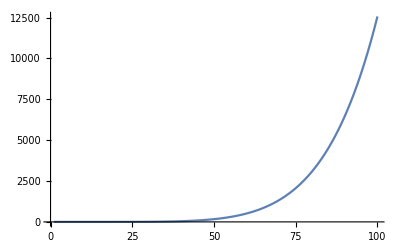

```mathematica
ListLinePlot[Table[diff[6,129383476557723,17234,18265,z],{z,0.001,0.1,0.001}]]
```

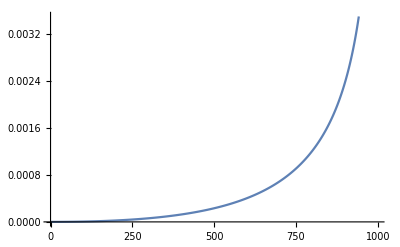

```mathematica
ListLinePlot[Table[flevel[2,1293834765577,17234,18265,z]+flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z]-(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2,{z,0.001,0.999,0.001}]]
```

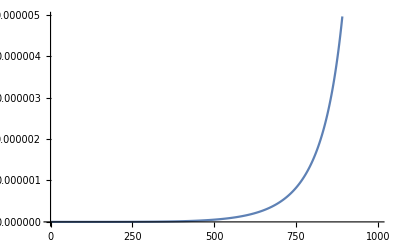

```mathematica
ListLinePlot[Table[(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2,{z,0.001,0.999,0.001}]]
```

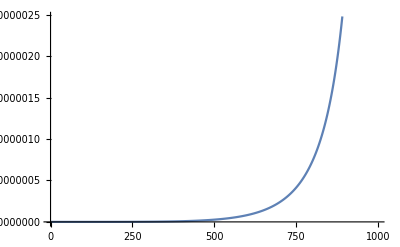

```mathematica
ListLinePlot[Table[(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2/2,{z,0.001,0.999,0.001}]]
```

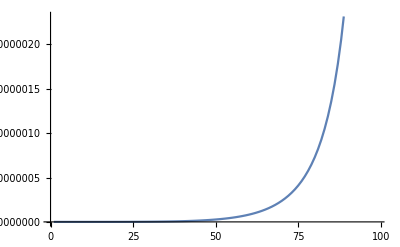

```mathematica
ListLinePlot[Table[flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z],{z,0.01,0.99,0.01}]]
```

```mathematica
fiz6[c_,h1_,h2_,z_]:=((14h1^2+h1)(14h2^2+h2)/(63c(70c+29))+(4h1 h2(c(70h1^2+42h1+8)+29h1^2-57h1-2)(c(70h2^2+42h2+8)+29h2^2-57h2-2))/(3c(2c-1)(5c+22)(7c+68)(70c+29)))*z^6*Hypergeometric2F1[6,6,12,z]
```

```mathematica
fiz6[c_,h1_,h2_,z_]:=((14h1^2+h1)(14h2^2+h2)/(63c(70c+29)))*z^6*Hypergeometric2F1[6,6,12,z]
```

```mathematica
1293834765577-17234*18265
```

1293519986567

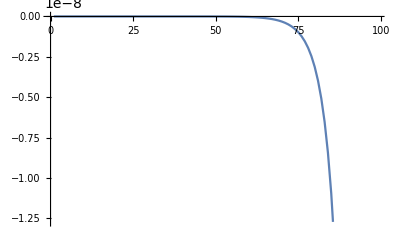

```mathematica
ListLinePlot[Table[flevel[4,1293834765577,17234,18265,z]+fiz6[1293834765577,17234,18265,z]-(2*17234 * 18265*z^2 Hypergeometric2F1[2,2,4,z]/1293834765577)^2/2,{z,0.01,0.99,0.01}]]
```

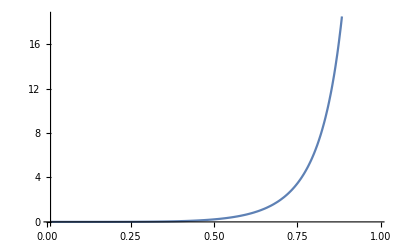

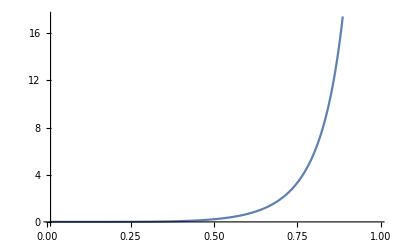

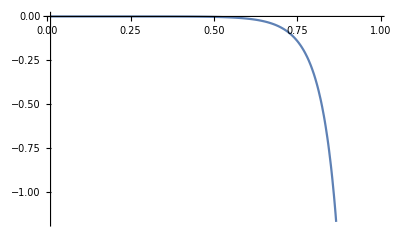

```mathematica
Plot[(z^2 Hypergeometric2F1[2,2,4,z])^2,{z,0.01,0.99}]
Plot[z^4 Hypergeometric2F1[4,4,8,z],{z,0.01,0.99}]
Plot[z^4 Hypergeometric2F1[4,4,8,z]-(z^2 Hypergeometric2F1[2,2,4,z])^2,{z,0.01,0.99}]
```

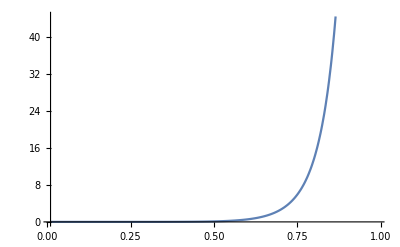

```mathematica
Plot[z^6 Hypergeometric2F1[6,6,12,z],{z,0.01,0.99}]
```

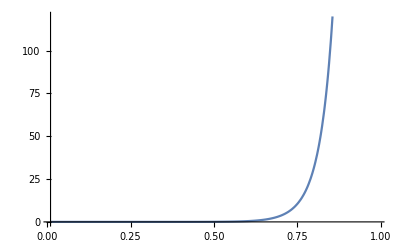

```mathematica
Plot[z^8 Hypergeometric2F1[8,8,16,z],{z,0.01,0.99}]
```